```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\spectro

```mathematica
fontSize=30;
```

### Longitudinal profile plot

```mathematica
data=Import["Longitudinal profile.csv","Dataset",HeaderLines->1];
```

```mathematica
density=Normal[data[All,"FWHM"]];
```

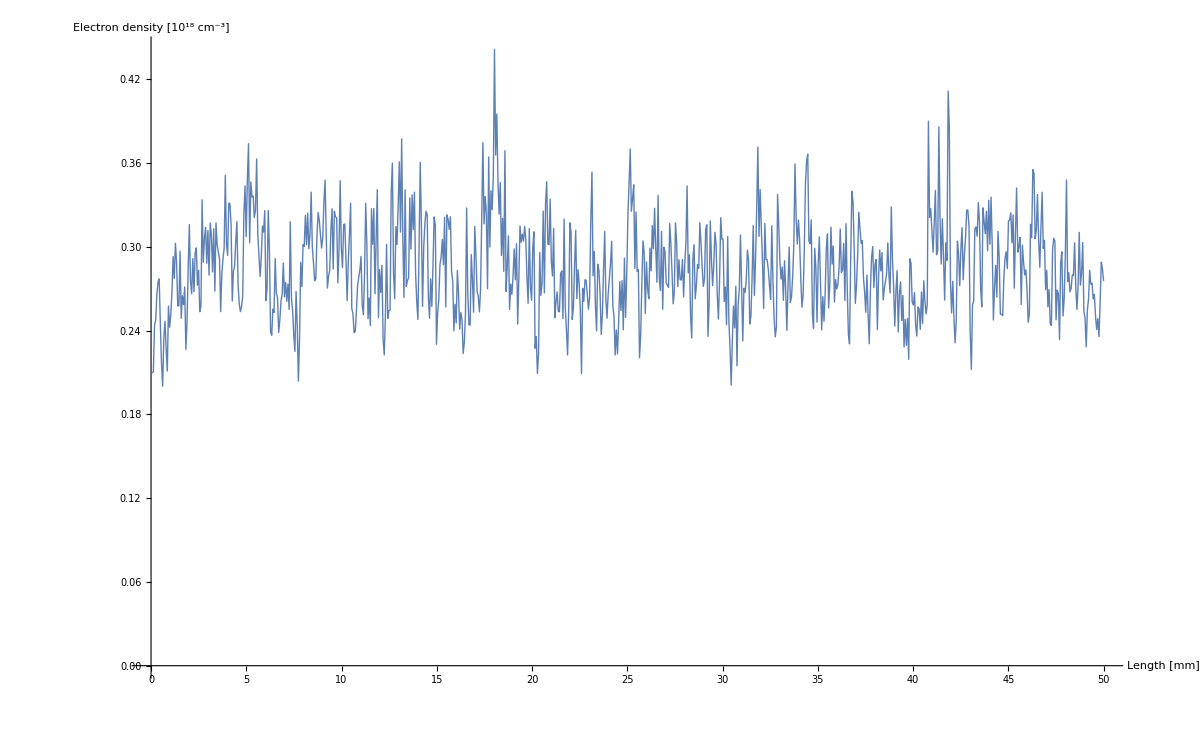

```mathematica
longitudinalProfile=ListLinePlot[((density*0.03)/5.4)^(3/2)
,PlotStyle->Thick
,Ticks->{Thread[{
Subdivide[Length[density],10],Subdivide[50,10]
}], Automatic}
,TicksStyle->Directive["Label", fontSize,Black]
,GridLines->{Automatic, Join[Thread[{
{.1,.2,.3,.4},
Table[Directive[Gray, Dashed,Thick],{j,4}]
}],{{Mean[((density*0.03)/5.4)^(3/2)],Directive[Red,Thickness[0.01],Dashing[{}]]}}]}
,GridLinesStyle->Directive[Gray, Dashed,Thick]
,Axes->True
,AxesStyle->Table[{Thickness[0.008],Black},{j,2}]
,AxesLabel->{Style["Length [mm]",fontSize],Style["Electron\ndensity [10^18 cm^-3]",fontSize,TextAlignment->Left]}
,PlotRangePadding->{None,Automatic}
,ImageSize->1200
]
```

```mathematica
Export["longitudinal_profile.pdf",longitudinalProfile]
Export["longitudinal_profile.png",longitudinalProfile]
```

longitudinal_profile.pdf

longitudinal_profile.png

```mathematica
SystemOpen["longitudinal_profile.png"]
```

```mathematica
StandardDeviation[((density*0.03)/5.4)^(3/2)]
```

0.0336531